# Brendan Philbin Simple Ising Model Trials

## Trial 1: N = 4, M = 100, β = 0.1, J = +1

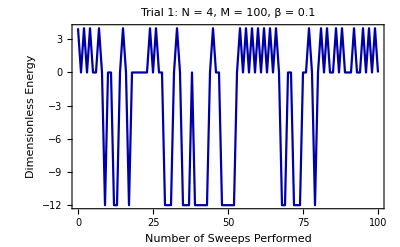

```mathematica
numSweeps=Range[0,100];
trial1={4,0,4,0,4,0,0,4,0,-12,0,0,-12,-12,0,4,0,-12,0,0,0,0,0,0,4,0,4,0,0,-12,-12,-12,0,4,0,-12,-12,-12,0,-12,-12,-12,-12,-12,0,4,0,0,-12,-12,-12,-12,-12,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,-12,-12,0,0,-12,-12,-12,0,0,4,0,-12,0,4,0,4,0,0,4,0,4,0,0,0,4,0,0,4,0,4,0,4,0};
trial1data=Transpose[{numSweeps,trial1}];
trial1plot=ListLinePlot[trial1data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 1: N = 4, M = 100, β = 0.1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 2: N = 4, M = 100, β = 1, J = +1

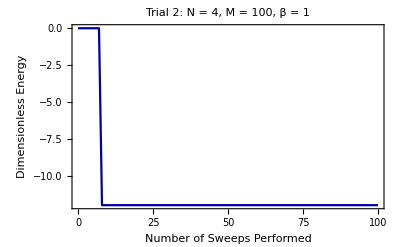

```mathematica
trial2={0,0,0,0,0,0,0,0,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12};
trial2data=Transpose[{numSweeps,trial2}];
trial2plot=ListLinePlot[trial2data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 2: N = 4, M = 100, β = 1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 3: N = 4, M = 100, β = 10, J = +1

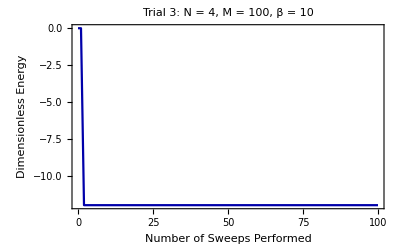

```mathematica
trial3={0,0,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12};
trial3data=Transpose[{numSweeps,trial3}];
trial3plot=ListLinePlot[trial3data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 3: N = 4, M = 100, β = 10", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 4: N = 16, M = 100, β = 0.1, J = +1

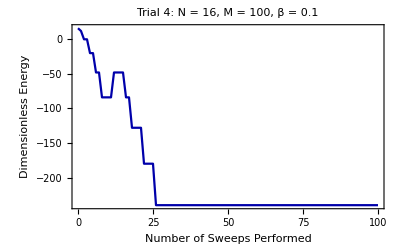

```mathematica
trial4={16,12,0,0,-20,-20,-48,-48,-84,-84,-84,-84,-48,-48,-48,-48,-84,-84,-128,-128,-128,-128,-180,-180,-180,-180,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240};
trial4data=Transpose[{numSweeps,trial4}];
trial4plot=ListLinePlot[trial4data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 4: N = 16, M = 100, β = 0.1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 5: N = 16, M = 100, β = 1, J = +1

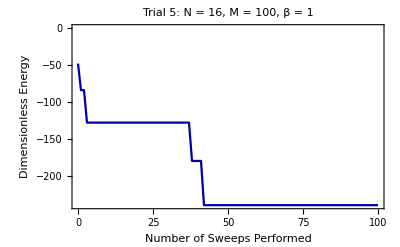

```mathematica
trial5={-48,-84,-84,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-128,-180,-180,-180,-180,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240};
trial5data=Transpose[{numSweeps,trial5}];
trial5plot=ListLinePlot[trial5data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 5: N = 16, M = 100, β = 1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 6: N = 16, M = 100, β = 10, J = +1

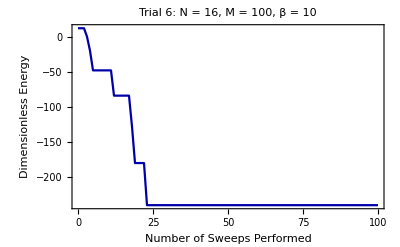

```mathematica
trial6={12,12,12,0,-20,-48,-48,-48,-48,-48,-48,-48,-84,-84,-84,-84,-84,-84,-128,-180,-180,-180,-180,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240,-240};
trial6data=Transpose[{numSweeps,trial6}];
trial6plot=ListLinePlot[trial6data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 6: N = 16, M = 100, β = 10", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 7: N = 64, M = 100, β = 0.1, J = +1

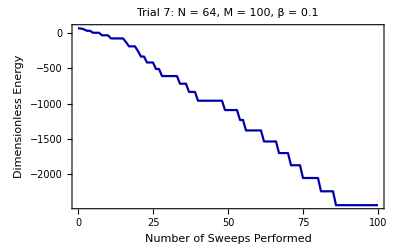

```mathematica
trial7={64,60,48,28,28,0,0,0,-36,-36,-36,-80,-80,-80,-80,-80,-132,-192,-192,-192,-260,-336,-336,-420,-420,-420,-512,-512,-612,-612,-612,-612,-612,-612,-720,-720,-720,-836,-836,-836,-960,-960,-960,-960,-960,-960,-960,-960,-960,-1092,-1092,-1092,-1092,-1092,-1232,-1232,-1380,-1380,-1380,-1380,-1380,-1380,-1536,-1536,-1536,-1536,-1536,-1700,-1700,-1700,-1700,-1872,-1872,-1872,-1872,-2052,-2052,-2052,-2052,-2052,-2052,-2240,-2240,-2240,-2240,-2240,-2436,-2436,-2436,-2436,-2436,-2436,-2436,-2436,-2436,-2436,-2436,-2436,-2436,-2436,-2436};
trial7data=Transpose[{numSweeps,trial7}];
trial7plot=ListLinePlot[trial7data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 7: N = 64, M = 100, β = 0.1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 8: N = 64, M = 100, β = 1, J = +1

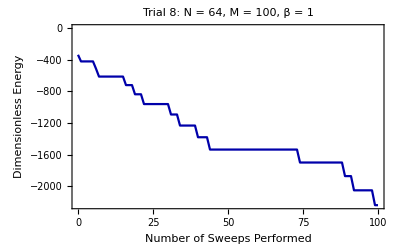

```mathematica
trial8={-336,-420,-420,-420,-420,-420,-512,-612,-612,-612,-612,-612,-612,-612,-612,-612,-720,-720,-720,-836,-836,-836,-960,-960,-960,-960,-960,-960,-960,-960,-960,-1092,-1092,-1092,-1232,-1232,-1232,-1232,-1232,-1232,-1380,-1380,-1380,-1380,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1700,-1700,-1700,-1700,-1700,-1700,-1700,-1700,-1700,-1700,-1700,-1700,-1700,-1700,-1700,-1872,-1872,-1872,-2052,-2052,-2052,-2052,-2052,-2052,-2052,-2240,-2240};
trial8data=Transpose[{numSweeps,trial8}];
trial8plot=ListLinePlot[trial8data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 8: N = 64, M = 100, β = 1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 9: N = 64, M = 100, β = 10, J = +1

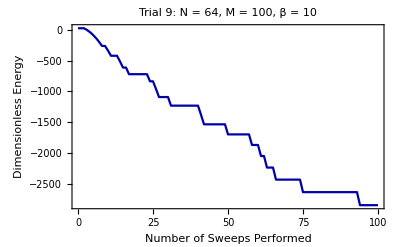

```mathematica
trial9={28,28,28,0,-36,-80,-132,-192,-260,-260,-336,-420,-420,-420,-512,-612,-612,-720,-720,-720,-720,-720,-720,-720,-836,-836,-960,-1092,-1092,-1092,-1092,-1232,-1232,-1232,-1232,-1232,-1232,-1232,-1232,-1232,-1232,-1380,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1536,-1700,-1700,-1700,-1700,-1700,-1700,-1700,-1700,-1872,-1872,-1872,-2052,-2052,-2240,-2240,-2240,-2436,-2436,-2436,-2436,-2436,-2436,-2436,-2436,-2436,-2640,-2640,-2640,-2640,-2640,-2640,-2640,-2640,-2640,-2640,-2640,-2640,-2640,-2640,-2640,-2640,-2640,-2640,-2640,-2852,-2852,-2852,-2852,-2852,-2852,-2852};
trial9data=Transpose[{numSweeps,trial9}];
trial9plot=ListLinePlot[trial9data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 9: N = 64, M = 100, β = 10", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 10: N = 8, M = 100, β = 0.1, J = +/-1

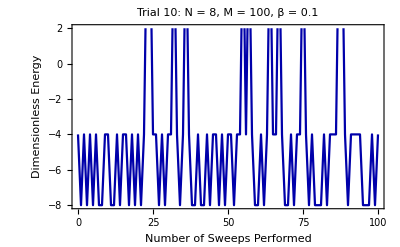

```mathematica
trial10={-4,-8,-4,-8,-4,-8,-4,-8,-8,-4,-4,-8,-8,-4,-8,-4,-4,-8,-4,-8,-4,-8,-4,8,8,-4,-4,-8,-4,-8,-4,-4,8,-4,-8,-4,8,-4,-8,-8,-4,-8,-8,-4,-8,-4,-4,-8,-4,-8,-4,-4,-8,-4,-4,8,-4,8,-4,-8,-8,-4,-8,-4,8,-4,-4,8,-4,-8,-8,-4,-8,-4,-4,8,-4,-8,-4,-8,-8,-8,-4,-8,-4,-4,-4,8,8,-4,-8,-4,-4,-4,-4,-8,-8,-8,-4,-8,-4};
trial10data=Transpose[{numSweeps,trial10}];
trial10plot=ListLinePlot[trial10data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 10: N = 8, M = 100, β = 0.1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 11: N = 8, M = 100, β = 1, J = +/-1

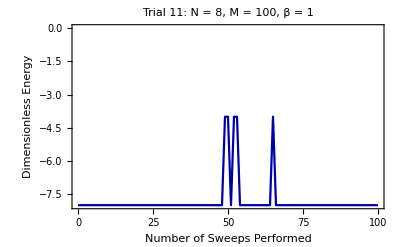

```mathematica
trial11={-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-4,-4,-8,-4,-4,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-4,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8};
trial11data=Transpose[{numSweeps,trial11}];
trial11plot=ListLinePlot[trial11data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 11: N = 8, M = 100, β = 1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 12: N = 8, M = 100, β = 10, J = +/-1

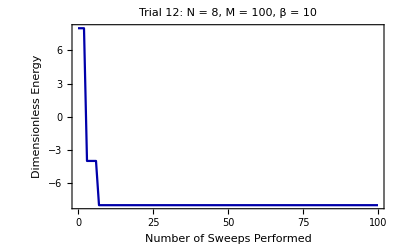

```mathematica
trial12={8,8,8,-4,-4,-4,-4,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8};
trial12data=Transpose[{numSweeps,trial12}];
trial12plot=ListLinePlot[trial12data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 12: N = 8, M = 100, β = 10", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```